```mathematica
ClearGlobal[]:=(ClearAll["Global`*"];Clear[Derivative];);
```

```mathematica
ClearGlobal[]
```

```mathematica
RemoveGlobal[]:=(ClearGlobal[];Remove["Global`*"];);
```

```mathematica
RemoveGlobal[]
```

## Recurrence Dynamics of Two-Loci Models

### The mating table

```mathematica
table :={{"T_1P_1×T_1P_1",Subscript[x, 11] Subscript[x, 11] Subscript[U, 11]/Subscript[t, 1],1,0,0,0}, (* squared *)
{"T_1P_1×T_1P_2",Subscript[x, 11] Subscript[x, 12] Subscript[U, 11]/Subscript[t, 1],1/2,1/2,0,0},
{"T_1P_1×T_2P_1",Subscript[x, 11] Subscript[x, 21] Subscript[U, 12]/Subscript[t, 2],1/2,0,1/2,0},
{"T_1P_1×T_2P_2",Subscript[x, 11] Subscript[x, 22] Subscript[U, 12]/Subscript[t, 2],1/2(1-r),1/2 r,1/2 r,1/2(1-r)},
{"T_1P_2×T_1P_1",Subscript[x, 12] Subscript[x, 11] Subscript[U, 21]/Subscript[t, 1],1/2,1/2 ,0,0},
{"T_1P_2×T_1P_2",Subscript[x, 12] Subscript[x, 12] Subscript[U, 21]/Subscript[t, 1],0,1 ,0,0}, (* squared *)
{"T_1P_2×T_2P_1",Subscript[x, 12] Subscript[x, 21] Subscript[U, 22]/Subscript[t, 2],1/2 r,1/2 (1-r) ,1/2 (1-r),1/2 r},
{"T_1P_2×T_2P_2",Subscript[x, 12] Subscript[x, 22] Subscript[U, 22]/Subscript[t, 2], 0,1/2 ,0,1/2},
{"T_2P_1×T_1P_1",Subscript[x, 21] Subscript[x, 11] Subscript[U, 11]/Subscript[t, 1], 1/2,0,1/2,0},
{"T_2P_1×T_1P_2",Subscript[x, 21] Subscript[x, 12] Subscript[U, 11]/Subscript[t, 1], 1/2r,1/2(1-r),1/2(1-r),1/2r},
{"T_2P_1×T_2P_1",Subscript[x, 21] Subscript[x, 21] Subscript[U, 12]/Subscript[t, 2],0,0,1,0}, (* squared *)
{"T_2P_1×T_2P_2",Subscript[x, 21] Subscript[x, 22] Subscript[U, 12]/Subscript[t, 2],0,0,1/2,1/2},
{"T_2P_2×T_1P_1",Subscript[x, 22] Subscript[x, 11] Subscript[U, 21]/Subscript[t, 1],1/2 (1-r),1/2r,1/2r,1/2(1-r)},
{"T_2P_2×T_1P_2", Subscript[x, 22] Subscript[x, 12] Subscript[U, 21]/Subscript[t, 1],0,1/2,0,1/2},
{"T_2P_2×T_2P_1", Subscript[x, 22] Subscript[x, 21] Subscript[U, 22]/Subscript[t, 2],0,0,1/2,1/2},
{"T_2P_2×T_2P_2", Subscript[x, 22] Subscript[x, 22] Subscript[U, 22]/Subscript[t, 2],0,0,0,1}   (* squared *)
}
```

```mathematica
header := {"♀×♂","Frequency","T_1P_1","T_1P_2","T_2P_1", "T_2P_2"}
```

```mathematica
Text[Grid[Prepend[table, header],Dividers->{{False,{False},False},{Black,Black,{False},Black}}]]
```

♀×♂ | Frequency | T_1P_1 | T_1P_2 | T_2P_1 | T_2P_2
T_1P_1×T_1P_1 | (U_11 x_11^2)/t_1 | 1 | 0 | 0 | 0
T_1P_1×T_1P_2 | (U_11 x_11 x_12)/t_1 | 1/2 | 1/2 | 0 | 0
T_1P_1×T_2P_1 | (U_12 x_11 x_21)/t_2 | 1/2 | 0 | 1/2 | 0
T_1P_1×T_2P_2 | (U_12 x_11 x_22)/t_2 | (1-r)/2 | r/2 | r/2 | (1-r)/2
T_1P_2×T_1P_1 | (U_21 x_11 x_12)/t_1 | 1/2 | 1/2 | 0 | 0
T_1P_2×T_1P_2 | (U_21 x_12^2)/t_1 | 0 | 1 | 0 | 0
T_1P_2×T_2P_1 | (U_22 x_12 x_21)/t_2 | r/2 | (1-r)/2 | (1-r)/2 | r/2
T_1P_2×T_2P_2 | (U_22 x_12 x_22)/t_2 | 0 | 1/2 | 0 | 1/2
T_2P_1×T_1P_1 | (U_11 x_11 x_21)/t_1 | 1/2 | 0 | 1/2 | 0
T_2P_1×T_1P_2 | (U_11 x_12 x_21)/t_1 | r/2 | (1-r)/2 | (1-r)/2 | r/2
T_2P_1×T_2P_1 | (U_12 x_21^2)/t_2 | 0 | 0 | 1 | 0
T_2P_1×T_2P_2 | (U_12 x_21 x_22)/t_2 | 0 | 0 | 1/2 | 1/2
T_2P_2×T_1P_1 | (U_21 x_11 x_22)/t_1 | (1-r)/2 | r/2 | r/2 | (1-r)/2
T_2P_2×T_1P_2 | (U_21 x_12 x_22)/t_1 | 0 | 1/2 | 0 | 1/2
T_2P_2×T_2P_1 | (U_22 x_21 x_22)/t_2 | 0 | 0 | 1/2 | 1/2
T_2P_2×T_2P_2 | (U_22 x_22^2)/t_2 | 0 | 0 | 0 | 1

```mathematica
Subscript[p, 1]:=1-Subscript[p, 2]
```

```mathematica
Subscript[t, 1]:=1-Subscript[t, 2]
```

```mathematica
Subscript[U, 11]:=1-Subscript[U, 12]
```

```mathematica
Subscript[U, 21] :=1-Subscript[U, 22]
```

```mathematica
Subscript[x, 21] :=Subscript[p, 1]-Subscript[x, 11]
```

```mathematica
Subscript[x, 22] :=Subscript[p, 2]-Subscript[x, 12]
```

```mathematica
Subscript[x, 12]:=Subscript[t, 1]-Subscript[x, 11]
```

```mathematica
Subscript[x, 22]:=Subscript[t, 2]-Subscript[x, 21]
```

### Finding recurrent formulas

Now the most important part -- finding values of three recurrent terms (t'_2, p'_2 , and D') in the next generation

```mathematica
Subscript[t', 2]=Simplify[Total[table[[All, 2]]*table[[All, 5]]+table[[All, 2]]*table[[All, 6]]]]
```

1/2 (t_2-(-1+p_2) U_12+p_2 U_22)

```mathematica
Subscript[p', 2] =Simplify[Total[table[[All, 2]]*table[[All, 4]]+table[[All, 2]]*table[[All, 6]]]/.{Subscript[x, 11]-> D+Subscript[t, 1] Subscript[p, 1]}]
```

((D-2 p_2) t_2+2 p_2 t_2^2+D (-1+p_2) U_12-D p_2 U_22)/(2 (-1+t_2) t_2)

```mathematica
D' = Simplify[(Total[table[[All, 2]]*table[[All, 6]]]-Subscript[t', 2]Subscript[p', 2])/.{Subscript[x, 11]-> D+Subscript[t, 1] Subscript[p, 1]}]
```

1/(4 (-1+t_2) t_2)(2 t_2 (D (-1+r)-(-1+p_2) (D-2 D r+r p_2) U_12+(D-r-2 D r) p_2 U_22+r p_2^2 U_22)+t_2^2 (D+2 r p_2^2 (U_12-U_22)+2 r p_2 (-U_12+U_22))+D ((-1+p_2)^2 U_12^2+U_22 (-2 D r+2 (-1+r) p_2+p_2^2 U_22)+2 U_12 (-1+r+D r-p_2^2 U_22+p_2 (1-r+U_22))))

Note the two {x_11→ D+t_1 p_1} replacements above (necessary because we want to express  p'_2 in terms of p_2 and D' in terms of D).

### Recurrence computation for random mating

First we enter the formulas for female preferences (copying the fully expanded U_22 formula from the previous notebook):

```mathematica
Subscript[U, 22]:=((1-s) Subscript[a, 2] Subscript[t, 2])/((1-s Subscript[t, 2]) (1-((1-s) Subscript[t, 2])/(1-s Subscript[t, 2])+((1-s) Subscript[a, 2] Subscript[t, 2])/(1-s Subscript[t, 2])))
```

```mathematica
Subscript[U, 21]:=1-Subscript[U, 22]
```

The expression for  U_12 is simply the previous expression with the {a_2→1}substitution (P_1females exhibit zero bias towards T_2 males):

```mathematica
Subscript[U, 12]=Subscript[U, 22]/.{Subscript[a, 2]->1}
```

((1-s) t_2)/(1-s t_2)

```mathematica
Subscript[U, 11] :=1-Subscript[U, 12]
```

The recurrence relation for linkage disequilibrium given {a_2→ 3.0,s→ 0.4}:

```mathematica
symbolReplace = {D->d[n], Subscript[t, 2]->x[n],Subscript[p, 2]->y[n], r->1/2}
```

{D→d[n],t_2→x[n],p_2→y[n],r→1/2}

```mathematica
args = {Subscript[a, 2]-> 3.0,s-> 0.4}
```

{a_2→3.,s→0.4}

```mathematica
f1[x0_, y0_]:=RecurrenceTable[{x[n+1] ==Simplify[Subscript[t', 2]/.symbolReplace]/.args,y[n+1]== Simplify[Subscript[p', 2]/.symbolReplace]/.args,d[n+1]==Simplify[D'/.symbolReplace]/.args,x[0]==x0,y[0]==y0, d[0]==0.001},{x,y,d},{n,1,100}]//Short
```

Finally let's make a scatter plot of X and Y pairs (corresponding to trait and preference) :

```mathematica
f1l[y0_] := f1[0.01, y0]
```

```mathematica
premap := Map[f1l, Table[0.05*i,{i,19}]]
```

```mathematica
m = Flatten[premap[[All,1]],1]
```

{{0.00830787,0.0498291,0.000556775},{0.00690012,0.0497339,0.000348208},1896,{1.,0.970935,3.1859×10^-9},{1.,0.970935,1.36516×10^-8}}
 |  |  |  |

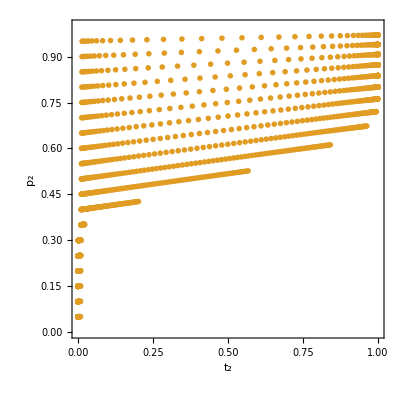

```mathematica
lrp =ListPlot[Transpose[{m[[All,1]], m[[All,2]]}],PlotRange->{{0,1},{0,1}},AspectRatio->1,Frame->True, FrameLabel->{Defer[Subscript[t,2]], Defer[Subscript[p,2]]},PlotStyle->{ColorData[97,"ColorList"][[2]],PointSize[0.01]},BaseStyle->{FontSize->12}]
```

Note that when female preference is high (0.8), it only takes a dozen or so generations to jump from low prevalence of the ornamented trait to it being found in majority of males. Changing the initial value of D doesn’t change much -- disequilibrium self-corrects after a few generations.

```mathematica
f1r[y0_]:=f1[0.99,y0]
```

```mathematica
premap := Map[f1r, Table[0.05*i,{i,19}]]
```

```mathematica
m = Flatten[premap[[All,1]],1]
```

{{0.986996,0.0496966,0.000778375},{0.983108,0.0494608,0.000671167},1896,{1.,0.950548,-0.0000101202},{1.,0.950546,-2.78968×10^-6}}
 |  |  |  |

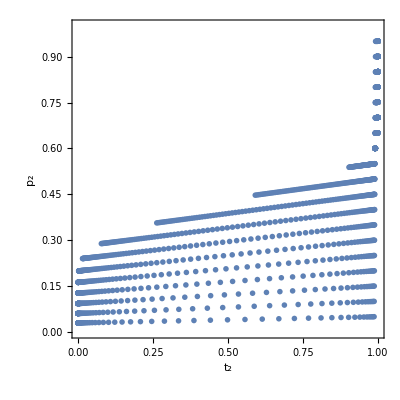

```mathematica
rlp =ListPlot[Transpose[{m[[All,1]], m[[All,2]]}],PlotRange->{{0,1},{0,1}},AspectRatio->1,Frame->True, FrameLabel->{Defer[Subscript[t,2]], Defer[Subscript[p,2]]},PlotStyle->{PointSize[0.01]},BaseStyle->{FontSize->12}]
```

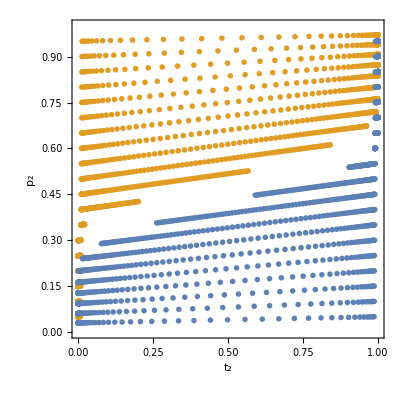

```mathematica
plot1 = Show[lrp, rlp]
```

### Recurrence computation for best-of-N case

Assuming c=1 (the female P_2 always chooses the ornamented male if one is present in the lek of N)

```mathematica
Subscript[U, 22]:=1-(1-((1-s) Subscript[t, 2])/(1-s Subscript[t, 2]))^N
```

```mathematica
Subscript[U, 21]:=1-Subscript[U, 22]
```

Copying the expanded expression for  U_12 from the previous section:

```mathematica
Subscript[U, 12]:=((1-s) Subscript[t, 2])/(1-s Subscript[t, 2])
```

```mathematica
Subscript[U, 11] :=1-Subscript[U, 12]
```

The recurrence relation for linkage disequilibrium given {N→ 3,s→ 0.4}:

```mathematica
symbolReplace = {D->d[n], Subscript[t, 2]->x[n],Subscript[p, 2]->y[n], r->1/2}
```

{D→d[n],t_2→x[n],p_2→y[n],r→1/2}

```mathematica
args = {N-> 3,s-> 0.4}
```

{N→3,s→0.4}

```mathematica
f1[x0_, y0_]:=RecurrenceTable[{x[n+1]==Simplify[Subscript[t', 2]/.symbolReplace]/.args,y[n+1]== Simplify[Subscript[p', 2]/.symbolReplace]/.args, d[n+1]== Simplify[D'/.symbolReplace]/.args,x[0]==x0,y[0]==y0, d[0]==0.001},{x,y,d},{n,1,100}]//Short
```

```mathematica
f1l[y0_] := f1[0.01, y0]
```

```mathematica
premap := Map[f1l, Table[0.05*i,{i,19}]]
```

```mathematica
m = Flatten[premap[[All,1]],1]
```

Power::infy: Infinite expression 1/0. encountered.

RecurrenceTable::excptn: Value {ComplexInfinity,1.,ComplexInfinity} is a numerical exception.

{{0.00831054,0.0498293,0.000558175},{0.00690417,0.0497341,0.000349763},1871,{1.,0.5,3.26807×10^-17},{1.,0.5,3.26807×10^-17}}
 |  |  |  |

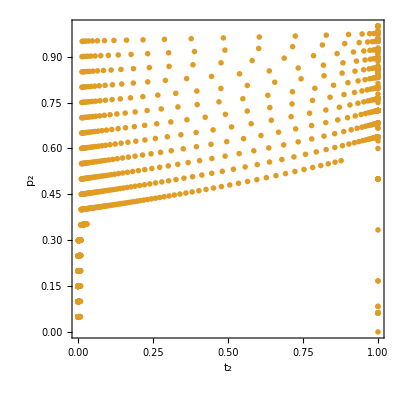

```mathematica
lrp =ListPlot[Transpose[{m[[All,1]], m[[All,2]]}],PlotRange->{{0,1},{0,1}},AspectRatio->1,Frame->True, FrameLabel->{Defer[Subscript[t,2]], Defer[Subscript[p,2]]},PlotStyle->{ColorData[97,"ColorList"][[2]],PointSize[0.01]},BaseStyle->{FontSize->12}]
```

```mathematica
f1r[y0_]:=f1[0.99,y0]
```

```mathematica
premap := Map[f1r, Table[0.05*i,{i,19}]]
```

```mathematica
m = Flatten[premap[[All,1]],1]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

RecurrenceTable::excptn: Value {ComplexInfinity,1.,Indeterminate} is a numerical exception.

{{0.987136,0.0497107,0.000837912},{0.983467,0.0494686,0.000787232},1849,{1.,1.,2.9655×10^-18},{1.,0.,8.47559×10^-19}}
 |  |  |  |

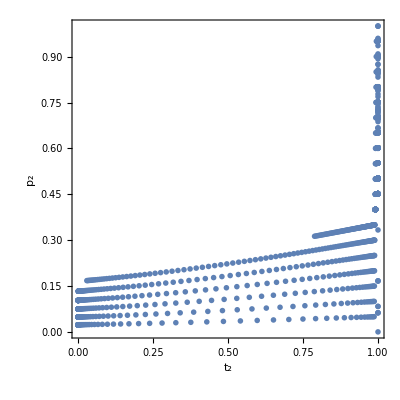

```mathematica
rlp =ListPlot[Transpose[{m[[All,1]], m[[All,2]]}],PlotRange->{{0,1},{0,1}},AspectRatio->1,Frame->True, FrameLabel->{Defer[Subscript[t,2]], Defer[Subscript[p,2]]},PlotStyle->{PointSize[0.01]},BaseStyle->{FontSize->12}]
```

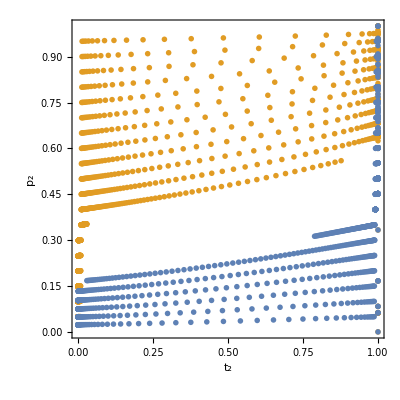

```mathematica
plot2 = Show[lrp, rlp]
```

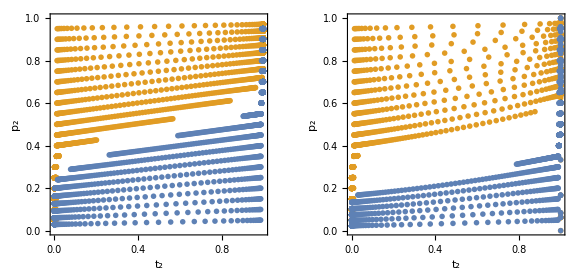

```mathematica
GraphicsRow[{plot1, plot2},ImageSize->Large]
```

#### Overlaying equilibria lines

The two formulas below are copied from the previous notebook:

```mathematica
eq1:={(s (-1+(1+(-1+s) Subscript[a, 2]) Subscript[t, 2]))/((-1+s) (-1+Subscript[a, 2]))}/. {s -> 0.4, Subscript[a, 2] -> 3}
```

```mathematica
eq2 := {-(s (-1+Subscript[t, 2]) Subscript[t, 2])/(1-((-1+Subscript[t, 2])/(-1+s Subscript[t, 2]))^n+Subscript[t, 2] (-1+s ((-1+Subscript[t, 2])/(-1+s Subscript[t, 2]))^n))}/. {s -> 0.4, c ->  1.0, n->3}
```

```mathematica
peq1 := Plot[eq1, {Subscript[t, 2], 0, 1}, PlotRange->{0,1},  PlotStyle->Black,FrameLabel->{Defer[Subscript[t, 2]], Defer[Subscript[p, 2]]},AspectRatio->1,Frame->True,BaseStyle->{FontSize->12}]
```

```mathematica
peq2:= Plot[eq2,
 {Subscript[t, 2], 0, 1}, PlotRange->{0,1}, PlotStyle->Black, FrameLabel->{Defer[Subscript[t, 2]], Defer[Subscript[p, 2]]},AspectRatio->1,Frame->True,BaseStyle->{FontSize->12}]
```

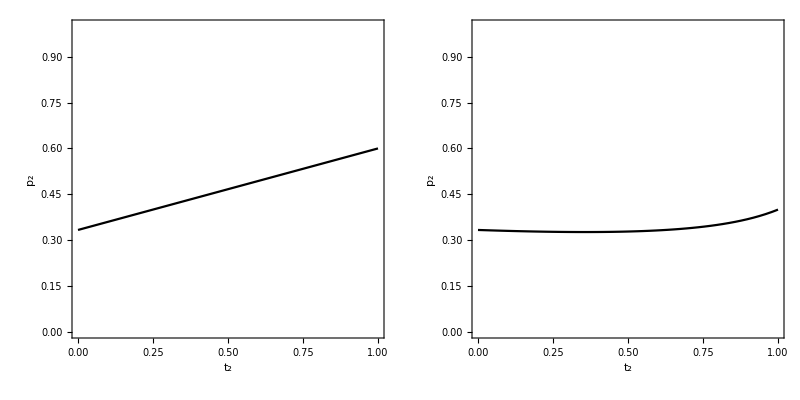

```mathematica
GraphicsRow[{peq1, peq2},Spacings->0]
```

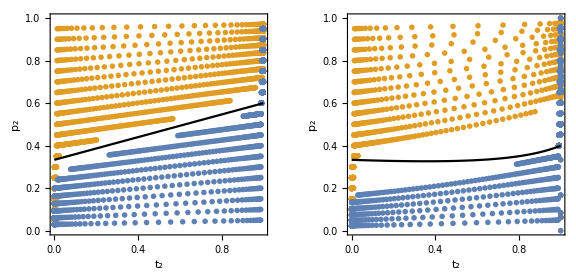

```mathematica
GraphicsRow[{Show[plot1, peq1], Show[plot2, peq2]},ImageSize->Large]
```